## Easy-Bot Live

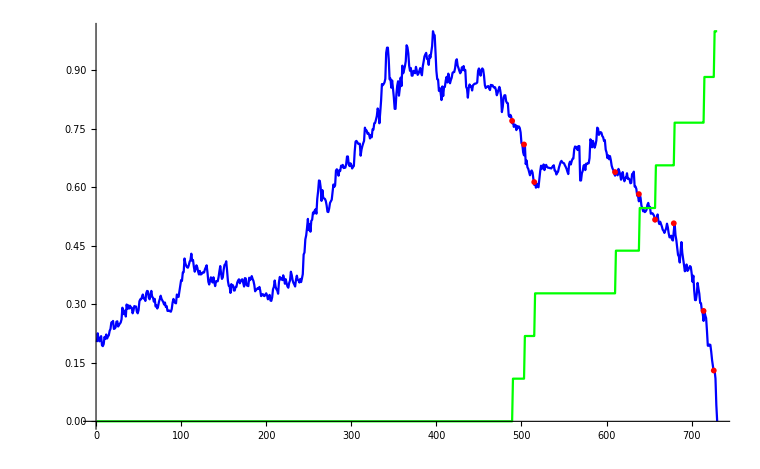

139.08       avg buy price

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

178.022       capitale utilizzato (buy)

24.8232       Guadagno massimo teorico

2.7525      Guadagno medio all-in all-out

-6.4915     Guadagno rispetto al capitale iniziale

-2.59256       Guadagno di Holding su capitale utilizzato

```mathematica
data2=Import["C:\\Users\\Feder\\Desktop\\Mango\\Programs\\python_bot\\easy_bot_real_money\\data_run\\data_sol_easybot_real_20_01_22.txt","Data"];
data = data2;
price = Transpose[data][[1]];
rsi = Transpose[data][[2]];
eth =  Transpose[data][[3]];
capital = Transpose[data][[4]];
len =Length[price];
start  = eth[[1]]*price[[1]] + capital[[1]];
now = eth[[-1]]*price[[-1]] +capital[[-1]];
holding= eth[[1]]*price[[-1]] + capital[[1]];
gainStart = now - start ; 
ethBought =0;
outCapital= 0;
ethSold =0;
buyPoint =ConstantArray[0,len];
sellPoint =ConstantArray[0,len];
inCapital = 0;
For[i=0,i<len,i++, 
If[eth[[i+1]]-eth[[i]]>0, 
x=eth[[i+1]]-eth[[i]];
 (*Print["Bought ",x, " ETH for ", price[[i+1]]] ;*)
ethBought += x;
outCapital += x*price[[i+1]];
buyPoint[[i]]=price[[i+1]];
];
If[eth[[i+1]]-eth[[i]]<0,
x=-eth[[i+1]]+eth[[i]]; 
(*Print["Sold ",x, " ETH for ", price[[i+1]]];*)
ethSold += x;
inCapital += x*price[[i+1]];
sellPoint[[i]]=price[[i+1]]
]]
sum=0;
n=0;
For[i=1,i<len-10,i++,For[j=10+i,j<len,j++,sum+=(price[[j]]/price[[i]]-1)*capital[[1]];n++;]];
Show[ListLinePlot[{(price-Min[price])/(Max[price]-Min[price]),
				(eth-Min[eth])/(Max[eth]-Min[eth])},
				PlotStyle->{Blue,Green,Yellow},PlotRange->{All,All}],
ListPlot[{(buyPoint-Min[price])/(Max[price]-Min[price]),
		(sellPoint-Min[price])/(Max[price]-Min[price])},
			PlotStyle->{Red,Green,PointSize[3]}]]
avgBuyPrice = outCapital/ethBought  "      avg buy price"
avgSellPrice = inCapital /ethSold  "      avg sell price"
outCapital  "      capitale utilizzato (buy)"
(Max[price]/Min[price]-1)*capital[[1]]  "      Guadagno massimo teorico"
sum/n "     Guadagno medio all-in all-out"
gainStart "    Guadagno rispetto al capitale iniziale"
(price[[len]]/price[[1]]-1)*outCapital "      Guadagno di Holding su capitale utilizzato"
```

## Easy-Bot Test

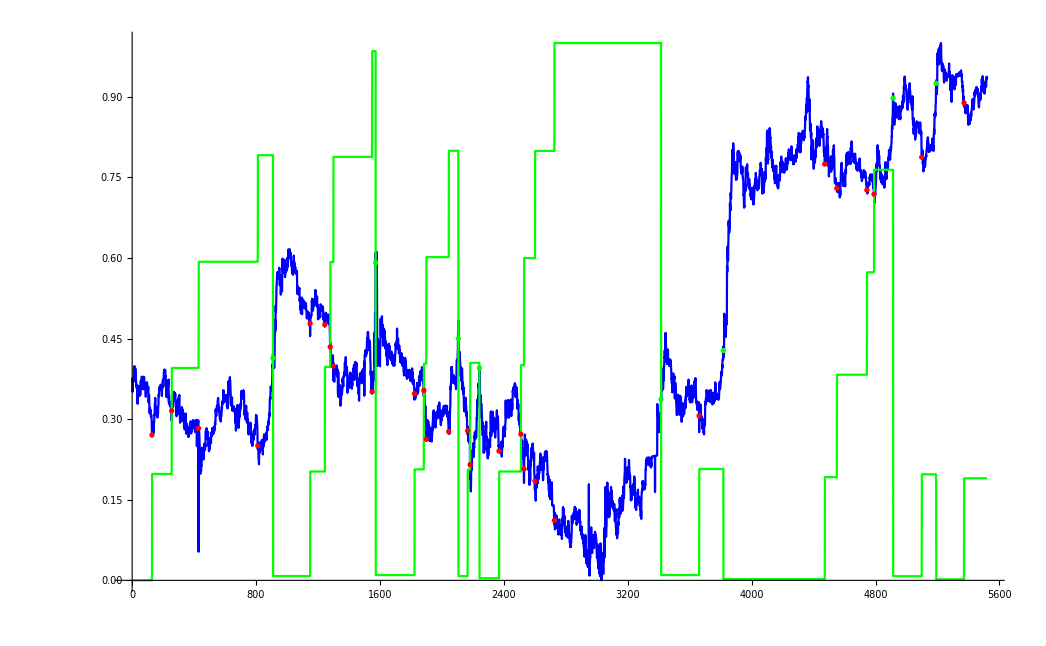

47166.6       avg buy price

47669.9       avg sell price

810.086       capitale utilizzato (buy)

86.6262       Guadagno massimo teorico

16.2081      Guadagno medio all-in all-out

9.64023     Guadagno rispetto al capitale iniziale

38.0764       Guadagno di Holding su capitale utilizzato

```mathematica
(******** Easy-Bot Test ********)
data2=Import["C:\\Users\\Feder\\Desktop\\Mango\\Programs\\python_bot\\easy_bot\\test\\data_test\\data_btc_easy_20_12_v4.txt","Data"];
data = data2;
price = Transpose[data][[1]];
rsi = Transpose[data][[2]];
eth =  Transpose[data][[3]];
capital = Transpose[data][[4]];
len =Length[price];
start  = eth[[1]]*price[[1]] + capital[[1]];
now = eth[[-1]]*price[[-1]] +capital[[-1]];
holding= eth[[1]]*price[[-1]] + capital[[1]];
gainStart = now - start ; 
ethBought =0;
outCapital= 0;
ethSold =0;
buyPoint =ConstantArray[0,len];
sellPoint =ConstantArray[0,len];
inCapital = 0;
For[i=0,i<len,i++, 
If[eth[[i+1]]-eth[[i]]>0, 
x=eth[[i+1]]-eth[[i]];
 (*Print["Bought ",x, " ETH for ", price[[i+1]]] ;*)
ethBought += x;
outCapital += x*price[[i+1]];
buyPoint[[i]]=price[[i+1]];
];
If[eth[[i+1]]-eth[[i]]<0,
x=-eth[[i+1]]+eth[[i]]; 
(*Print["Sold ",x, " ETH for ", price[[i+1]]];*)
ethSold += x;
inCapital += x*price[[i+1]];
sellPoint[[i]]=price[[i+1]]
]]
sum=0;
n=0;
For[i=1,i<len-10,i++,For[j=10+i,j<len,j++,sum+=(price[[j]]/price[[i]]-1)*capital[[1]];n++;]];
Show[ListLinePlot[{(price-Min[price])/(Max[price]-Min[price]),
				(eth-Min[eth])/(Max[eth]-Min[eth])},
				PlotStyle->{Blue,Green,Yellow},PlotRange->{All,All}],
ListPlot[{(buyPoint-Min[price])/(Max[price]-Min[price]),
		(sellPoint-Min[price])/(Max[price]-Min[price])},
			PlotStyle->{Red,Green}]]
avgBuyPrice = outCapital/ethBought  "      avg buy price"
avgSellPrice = inCapital /ethSold  "      avg sell price"
outCapital  "      capitale utilizzato (buy)"
(Max[price]/Min[price]-1)*capital[[1]]  "      Guadagno massimo teorico"
sum/n "     Guadagno medio all-in all-out"
gainStart "    Guadagno rispetto al capitale iniziale"
(price[[len]]/price[[1]]-1)*outCapital "      Guadagno di Holding su capitale utilizzato"
```

## Buy & Sell

```mathematica
(****** Buy & Sell ******)
ethBought =0;
outCapital= 0;
ethSold =0;
inCapital = 0;
For[i=0,i<len,i++, 
If[eth[[i+1]]-eth[[i]]>0, 
x=eth[[i+1]]-eth[[i]];
 Print["Bought ",x, " ETH for ", price[[i+1]]] ;
ethBought += x;
outCapital += x*price[[i+1]];
];
If[eth[[i+1]]-eth[[i]]<0,
x=-eth[[i+1]]+eth[[i]]; 
Print["Sold ",x, " ETH for ", price[[i+1]]];
ethSold += x;
inCapital += x*price[[i+1]];
];]
outCapital/ethBought  "(average BUY price)"
inCapital /ethSold "(average SELL price)"
outCapital
inCapital
```

Bought 0.11 ETH for 133.34

133.34 (average BUY price)

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

14.6674

0

## Moving Avgs

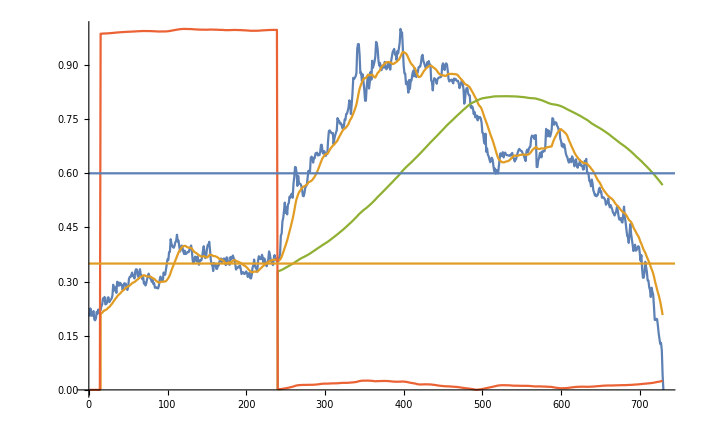

```mathematica
(****** Moving Avgs ******)
price1 =ConstantArray[0,Length[price]-1];
rsi1 =ConstantArray[0,Length[price]-1];
price3 =ConstantArray[0,Length[price]-1];
madeep1 =15;
madeep2=20;
madeep3=240;
For[i=1,i<Length[price],i++,
If[i<madeep1,
price1[ [i]]=0;,
sum=0;For[ j=0,j<madeep1,j++, sum += price[[i-j]] ];price1[[i]]=sum/madeep1;
]]
For[i=1,i<Length[rsi],i++,
If[i<madeep2,
rsi1[ [i]]=0;,
sum=0;For[ j=0,j<madeep2,j++, sum += price[[i-j]] ];price1[[i]]=sum/madeep2;
]]
For[i=1,i<Length[price],i++,
If[i<madeep3,
price3[ [i]]=0;,
sum=0;For[ j=0,j<madeep3,j++, sum += price[[i-j]] ];price3[[i]]=sum/madeep3;
]]
Show[ListLinePlot[{(price-Min[price])/(Max[price]-Min[price]),(price1-Min[price])/(Max[price]-Min[price]),(price3-Min[price])/(Max[price]-Min[price]),Abs[(price1-price3)/Max[price1-price3]]},PlotRange->{{0,len},{0,1}}],Plot[{0.6,0.35},{x,0,3000}]]
```

```mathematica
(***** Bands *****)
len=700;
upBand=ConstantArray[0,3000];
downBand=ConstantArray[0,3000];
avg=ConstantArray[0,3000];
For[l=20,l<len,l++,
nlm=NonlinearModelFit[Take[price,l],a + b*t,{a,b },t];
f=nlm["Function"];
res=nlm["FitResiduals"];
dev=Mean[Abs[res]];
upBand [[l]]=f[l]+dev;
downBand [[l]]=f[l]-dev;
avg[[l]]=f[l];]
Show[ListPlot[{(price-Min[price])/(Max[price]-Min[price]),(avg-Min[price])/(Max[price]-Min[price]),(upBand-Min[price])/(Max[price]-Min[price]),(downBand-Min[price])/(Max[price]-Min[price])},PlotRange->{{0,len},{0,1}},PlotStyle->{Blue,Yellow,Green,Red,White}],ListLinePlot[rsi/100],Plot[{0.6,0.35},{x,0,len}]]
```

Take::take: Cannot take positions 1 through 731 in {135.96,136.18,136.02,135.98,136.07,136.11,135.88,135.86,135.91,136.09,136.04,136.15,136.05,136.1,136.13,136.24,136.29,136.45,136.44,136.49,136.29,136.3,136.33,136.47,136.48,136.35,136.39,136.42,136.45,136.53,136.82,136.66,136.68,136.75,136.6,136.9,136.79,136.88,136.8,136.87,136.81,136.82,136.68,136.75,136.86,136.85,136.85,136.72,136.68,136.76,«680»}.

NonlinearModelFit::fitd: First argument Take[{135.96,136.18,136.02,135.98,136.07,136.11,135.88,135.86,135.91,136.09,136.04,136.15,136.05,136.1,136.13,136.24,136.29,136.45,136.44,136.49,136.29,136.3,136.33,136.47,136.48,136.35,136.39,136.42,136.45,136.53,136.82,136.66,136.68,136.75,136.6,136.9,136.79,136.88,136.8,136.87,136.81,136.82,136.68,136.75,136.86,136.85,136.85,136.72,136.68,136.76,«680»},731] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

Take::take: Cannot take positions 1 through 732 in {135.96,136.18,136.02,135.98,136.07,136.11,135.88,135.86,135.91,136.09,136.04,136.15,136.05,136.1,136.13,136.24,136.29,136.45,136.44,136.49,136.29,136.3,136.33,136.47,136.48,136.35,136.39,136.42,136.45,136.53,136.82,136.66,136.68,136.75,136.6,136.9,136.79,136.88,136.8,136.87,136.81,136.82,136.68,136.75,136.86,136.85,136.85,136.72,136.68,136.76,«680»}.

Take::take: Cannot take positions 1 through 733 in {135.96,136.18,136.02,135.98,136.07,136.11,135.88,135.86,135.91,136.09,136.04,136.15,136.05,136.1,136.13,136.24,136.29,136.45,136.44,136.49,136.29,136.3,136.33,136.47,136.48,136.35,136.39,136.42,136.45,136.53,136.82,136.66,136.68,136.75,136.6,136.9,136.79,136.88,136.8,136.87,136.81,136.82,136.68,136.75,136.86,136.85,136.85,136.72,136.68,136.76,«680»}.

General::stop: Further output of Take::take will be suppressed during this calculation.

NonlinearModelFit::fitd: First argument Take[{135.96,136.18,136.02,135.98,136.07,136.11,135.88,135.86,135.91,136.09,136.04,136.15,136.05,136.1,136.13,136.24,136.29,136.45,136.44,136.49,136.29,136.3,136.33,136.47,136.48,136.35,136.39,136.42,136.45,136.53,136.82,136.66,136.68,136.75,136.6,136.9,136.79,136.88,136.8,136.87,136.81,136.82,136.68,136.75,136.86,136.85,136.85,136.72,136.68,136.76,«680»},731] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::fitd: First argument Take[{135.96,136.18,136.02,135.98,136.07,136.11,135.88,135.86,135.91,136.09,136.04,136.15,136.05,136.1,136.13,136.24,136.29,136.45,136.44,136.49,136.29,136.3,136.33,136.47,136.48,136.35,136.39,136.42,136.45,136.53,136.82,136.66,136.68,136.75,136.6,136.9,136.79,136.88,136.8,136.87,136.81,136.82,136.68,136.75,136.86,136.85,136.85,136.72,136.68,136.76,«680»},732] in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit::fitd: First argument Take[{135.96,136.18,136.02,135.98,136.07,136.11,135.88,135.86,135.91,136.09,136.04,136.15,136.05,136.1,136.13,136.24,136.29,136.45,136.44,136.49,136.29,136.3,136.33,136.47,136.48,136.35,136.39,136.42,136.45,136.53,136.82,136.66,136.68,136.75,136.6,136.9,136.79,136.88,136.8,136.87,136.81,136.82,136.68,136.75,136.86,136.85,136.85,136.72,136.68,136.76,«680»},733] in NonlinearModelFit is not a list or a rectangular array.

General::stop: Further output of NonlinearModelFit::fitd will be suppressed during this calculation.

$Aborted